```mathematica
Clear["Global`*"]
```

```mathematica
Clear[a,b,u1,u2,α,β]
(*KT and diffusion constant are set to one*)
KT = 1;
d=1;
RSink = 1;
W = {{-w12, w21},{w12,-w21}};
EvecWtmp={{w21/w12,1},{-1,1}};
stmp = Transpose[{Normalize[EvecWtmp[[1]]],Normalize[EvecWtmp[[2]]]}] ;
invstmp = Simplify[Assuming[{w12>0, w21>0},Inverse[stmp]]];
DiagW = Simplify[invstmp.W.stmp];
BCu = {{Exp[u1/kt],0},{0,Exp[u2/kt]}};
(*Time scale of switching is given by α, ratio of rates is given by β to simplify system of linear equations*)
(* α is basically the sum of the eigenvalues divided by D *)
(* β is the ratio between the eigenvalues -does not matter if divided by D since they cancel out! *)
DiagW = DiagW/.-w12-w21 ->α
EvecW=EvecWtmp/.w21/w12 ->β
s = Transpose[{Normalize[EvecW[[1]]],Normalize[EvecW[[2]]]}] 
invs=Simplify[Assuming[{w12>0, w21>0},Inverse[s]]]
```

{{0,0},{0,α}}

{{β,1},{-1,1}}

{{β/(√(1+Abs[β]^2)),-1/(√2)},{1/(√(1+Abs[β]^2)),1/(√2)}}

{{(√(1+Abs[β]^2))/(1+β),(√(1+Abs[β]^2))/(1+β)},{-(√2)/(1+β),(√2 β)/(1+β)}}

```mathematica
BCu = {{Exp[u1/KT],0},{0,Exp[u2/KT]}};
```

```mathematica
rhodash[r_] = {{1, 1/r, 0, 0},{0, 0, Exp[-Sqrt[Abs[DiagW[[2,2]]]/d]r]/r,Exp[Sqrt[Abs[DiagW[[2,2]]]/d]r]/r}}
```

{{1,1/r,0,0},{0,0,ⅇ^(-r √Abs[α])/r,ⅇ^(r √Abs[α])/r}}

```mathematica
(* These are the "NEW" boundary conditions *)
lgs1 = Join[4π RSink^2 rhodash'[RSink]-kReact rhodash[RSink],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];
(* This was the old boundary condition *)
(*lgs1 = Join[rhodash[RSink],{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},2];*)
lgs2 = Join[rhodash[a], -invs.BCu.s.rhodash[a], {{0,0,0,0},{0,0,0,0}},2];
lgs3 = Join[rhodash'[a],-rhodash'[a],{{0,0,0,0},{0,0,0,0}},2];
lgs4= Join[{{0,0,0,0},{0,0,0,0}},invs.BCu.s.rhodash[b],-rhodash[b],2];
lgs5 = Join[{{0,0,0,0},{0,0,0,0}},rhodash'[b],-rhodash'[b],2];
lgs6 = Join[{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{1,0,0,0},{0,0,0,Infinity}},2];
lgs = Join[lgs1, lgs2, lgs3, lgs4,lgs5,lgs6,1];
lgs = lgs[[1;;11,1;;11]]
```

{{-kReact,-kReact-4 π,0,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-√Abs[α]) kReact+4 π (-ⅇ^(-√Abs[α])-ⅇ^(-√Abs[α]) √Abs[α]),-ⅇ^(√Abs[α]) kReact+4 π (-ⅇ^(√Abs[α])+ⅇ^(√Abs[α]) √Abs[α]),0,0,0,0,0,0,0},{1,1/a,0,0,-ⅇ^u2/(1+β)-(ⅇ^u1 β)/(1+β),-(ⅇ^u2/(1+β)+(ⅇ^u1 β)/(1+β))/a,-(ⅇ^(-a √Abs[α]) (-(ⅇ^u1 √(1+Abs[β]^2))/(√2 (1+β))+(ⅇ^u2 √(1+Abs[β]^2))/(√2 (1+β))))/a,-(ⅇ^(a √Abs[α]) (-(ⅇ^u1 √(1+Abs[β]^2))/(√2 (1+β))+(ⅇ^u2 √(1+Abs[β]^2))/(√2 (1+β))))/a,0,0,0},{0,0,ⅇ^(-a √Abs[α])/a,ⅇ^(a √Abs[α])/a,(√2 ⅇ^u1 β)/((1+β) √(1+Abs[β]^2))-(√2 ⅇ^u2 β)/((1+β) √(1+Abs[β]^2)),-(-(√2 ⅇ^u1 β)/((1+β) √(1+Abs[β]^2))+(√2 ⅇ^u2 β)/((1+β) √(1+Abs[β]^2)))/a,-(ⅇ^(-a √Abs[α]) (ⅇ^u1/(1+β)+(ⅇ^u2 β)/(1+β)))/a,-(ⅇ^(a √Abs[α]) (ⅇ^u1/(1+β)+(ⅇ^u2 β)/(1+β)))/a,0,0,0},{0,-1/a^2,0,0,0,1/a^2,0,0,0,0,0},{0,0,-ⅇ^(-a √Abs[α])/a^2-(ⅇ^(-a √Abs[α]) √Abs[α])/a,-ⅇ^(a √Abs[α])/a^2+(ⅇ^(a √Abs[α]) √Abs[α])/a,0,0,ⅇ^(-a √Abs[α])/a^2+(ⅇ^(-a √Abs[α]) √Abs[α])/a,ⅇ^(a √Abs[α])/a^2-(ⅇ^(a √Abs[α]) √Abs[α])/a,0,0,0},{0,0,0,0,ⅇ^u2/(1+β)+(ⅇ^u1 β)/(1+β),(ⅇ^u2/(1+β)+(ⅇ^u1 β)/(1+β))/b,(ⅇ^(-b √Abs[α]) (-(ⅇ^u1 √(1+Abs[β]^2))/(√2 (1+β))+(ⅇ^u2 √(1+Abs[β]^2))/(√2 (1+β))))/b,(ⅇ^(b √Abs[α]) (-(ⅇ^u1 √(1+Abs[β]^2))/(√2 (1+β))+(ⅇ^u2 √(1+Abs[β]^2))/(√2 (1+β))))/b,-1,-1/b,0},{0,0,0,0,-(√2 ⅇ^u1 β)/((1+β) √(1+Abs[β]^2))+(√2 ⅇ^u2 β)/((1+β) √(1+Abs[β]^2)),(-(√2 ⅇ^u1 β)/((1+β) √(1+Abs[β]^2))+(√2 ⅇ^u2 β)/((1+β) √(1+Abs[β]^2)))/b,(ⅇ^(-b √Abs[α]) (ⅇ^u1/(1+β)+(ⅇ^u2 β)/(1+β)))/b,(ⅇ^(b √Abs[α]) (ⅇ^u1/(1+β)+(ⅇ^u2 β)/(1+β)))/b,0,0,-ⅇ^(-b √Abs[α])/b},{0,0,0,0,0,-1/b^2,0,0,0,1/b^2,0},{0,0,0,0,0,0,-ⅇ^(-b √Abs[α])/b^2-(ⅇ^(-b √Abs[α]) √Abs[α])/b,-ⅇ^(b √Abs[α])/b^2+(ⅇ^(b √Abs[α]) √Abs[α])/b,0,0,ⅇ^(-b √Abs[α])/b^2+(ⅇ^(-b √Abs[α]) √Abs[α])/b},{0,0,0,0,0,0,0,0,1,0,0}}

```mathematica
c =TimeConstrained[Assuming[{w12>0&& w21>0&&d>0&&KT>0&&b>a>RSink>0&&kReact>0}, LinearSolve[lgs,Transpose[{{0,0,0,0,0,0,0,0,0,0,1}}]]],Infinity];
```

LinearSolve::optx: Unknown option TimeConstraint in LinearSolve[{{-kReact, -kReact - 4\ π, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -ⅇ^-Power[« 2 »]\ kReact + 4\ π\ (-Power[« 2 »] - Power[« 2 »]\ Power[« 2 »]), -ⅇ^√Abs[« 1 »]\ kReact + 4\ π\ (-Power[« 2 »] + Power[« 2 »]\ Power[« 2 »]), 0, 0, 0, 0, 0, 0, 0}, « 8 », {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}}, {{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {1}}, TimeConstraint → 3000].

$Aborted

$Aborted

```mathematica
c = Join[c,{{0}}];

rhodash1[r_] = rhodash[r].c[[1;;4]];
rhodash2[r_] = rhodash[r].c[[5;;8]];
rhodash3[r_] = rhodash[r].c[[9;;12]];
n = Limit[Total[Total[s.rhodash3[r]]],r->Infinity]
(*Calculate density profiles*)
rho1[r_] = s.rhodash1[r]/n;
rho2[r_] = s.rhodash2[r]/n;
rho3[r_] = s.rhodash3[r]/n;
(*Calculate mean density profiles*)
rhom1[r_] =Part[rho1[r],1]+ Part[rho1[r],2];
rhom2[r_] =Part[rho2[r],1]+ Part[rho2[r],2];
rhom3[r_] =Part[rho3[r],1]+ Part[rho3[r],2];
(* Calculate absorption rate,this is just kReact x rho[RSink] for this problem, as deduced from B.C. *)
```

```mathematica
Clear[u1,u2,α, β, a, b,kReact]
k:=  Simplify[Total[rhom1[RSink]],TimeConstraint->Infinity];
k
```

({{β/(√(1+Abs[β]^2)),β/(√(1+Abs[β]^2)),-ⅇ^(-√Abs[α])/(√2),-ⅇ^(√Abs[α])/(√2)},{1/(√(1+Abs[β]^2)),1/(√(1+Abs[β]^2)),ⅇ^(-√Abs[α])/(√2),ⅇ^(√Abs[α])/(√2)}}.Join[LinearSolve[{{-kReact,-kReact-4 π,0,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-√Abs[α]) (kReact+4 π+4 π √Abs[α]),ⅇ^(√Abs[α]) (-kReact-4 π+4 π √Abs[α]),0,0,0,0,0,0,0},{1,1/a,0,0,-(ⅇ^u2+ⅇ^u1 β)/(1+β),-(ⅇ^u2+ⅇ^u1 β)/(a+a β),(ⅇ^(-a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),(ⅇ^(a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),0,0,0},{0,0,ⅇ^(-a √Abs[α])/a,ⅇ^(a √Abs[α])/a,(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),(√2 (ⅇ^u1-ⅇ^u2) β)/(a (1+β) √(1+Abs[β]^2)),-(ⅇ^(-a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),-(ⅇ^(a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),0,0,0},{0,-1/a^2,0,0,0,1/a^2,0,0,0,0,0},{0,0,-(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (-1+a √Abs[α]))/a^2,0,0,(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (1-a √Abs[α]))/a^2,0,0,0},{0,0,0,0,(ⅇ^u2+ⅇ^u1 β)/(1+β),(ⅇ^u2+ⅇ^u1 β)/(b+b β),(ⅇ^(-b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),(ⅇ^(b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),-1,-1/b,0},{0,0,0,0,-(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),-(√2 (ⅇ^u1-ⅇ^u2) β)/(b (1+β) √(1+Abs[β]^2)),(ⅇ^(-b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),(ⅇ^(b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),0,0,-ⅇ^(-b √Abs[α])/b},{0,0,0,0,0,-1/b^2,0,0,0,1/b^2,0},{0,0,0,0,0,0,-(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2,(ⅇ^(b √Abs[α]) (-1+b √Abs[α]))/b^2,0,0,(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2},{0,0,0,0,0,0,0,0,1,0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}},TimeConstraint→3000],{{0}}]⟦1;;4⟧ (1+β+4 √(1+Abs[β]^2) Join[LinearSolve[{{-kReact,-kReact-4 π,0,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-√Abs[α]) (kReact+4 π+4 π √Abs[α]),ⅇ^(√Abs[α]) (-kReact-4 π+4 π √Abs[α]),0,0,0,0,0,0,0},{1,1/a,0,0,-(ⅇ^u2+ⅇ^u1 β)/(1+β),-(ⅇ^u2+ⅇ^u1 β)/(a+a β),(ⅇ^(-a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),(ⅇ^(a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),0,0,0},{0,0,ⅇ^(-a √Abs[α])/a,ⅇ^(a √Abs[α])/a,(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),(√2 (ⅇ^u1-ⅇ^u2) β)/(a (1+β) √(1+Abs[β]^2)),-(ⅇ^(-a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),-(ⅇ^(a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),0,0,0},{0,-1/a^2,0,0,0,1/a^2,0,0,0,0,0},{0,0,-(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (-1+a √Abs[α]))/a^2,0,0,(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (1-a √Abs[α]))/a^2,0,0,0},{0,0,0,0,(ⅇ^u2+ⅇ^u1 β)/(1+β),(ⅇ^u2+ⅇ^u1 β)/(b+b β),(ⅇ^(-b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),(ⅇ^(b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),-1,-1/b,0},{0,0,0,0,-(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),-(√2 (ⅇ^u1-ⅇ^u2) β)/(b (1+β) √(1+Abs[β]^2)),(ⅇ^(-b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),(ⅇ^(b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),0,0,-ⅇ^(-b √Abs[α])/b},{0,0,0,0,0,-1/b^2,0,0,0,1/b^2,0},{0,0,0,0,0,0,-(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2,(ⅇ^(b √Abs[α]) (-1+b √Abs[α]))/b^2,0,0,(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2},{0,0,0,0,0,0,0,0,1,0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}},TimeConstraint→3000],{{0}}]⟦9;;12⟧))/(2 Join[LinearSolve[{{-kReact,-kReact-4 π,0,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-√Abs[α]) (kReact+4 π+4 π √Abs[α]),ⅇ^(√Abs[α]) (-kReact-4 π+4 π √Abs[α]),0,0,0,0,0,0,0},{1,1/a,0,0,-(ⅇ^u2+ⅇ^u1 β)/(1+β),-(ⅇ^u2+ⅇ^u1 β)/(a+a β),(ⅇ^(-a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),(ⅇ^(a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),0,0,0},{0,0,ⅇ^(-a √Abs[α])/a,ⅇ^(a √Abs[α])/a,(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),(√2 (ⅇ^u1-ⅇ^u2) β)/(a (1+β) √(1+Abs[β]^2)),-(ⅇ^(-a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),-(ⅇ^(a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),0,0,0},{0,-1/a^2,0,0,0,1/a^2,0,0,0,0,0},{0,0,-(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (-1+a √Abs[α]))/a^2,0,0,(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (1-a √Abs[α]))/a^2,0,0,0},{0,0,0,0,(ⅇ^u2+ⅇ^u1 β)/(1+β),(ⅇ^u2+ⅇ^u1 β)/(b+b β),(ⅇ^(-b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),(ⅇ^(b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),-1,-1/b,0},{0,0,0,0,-(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),-(√2 (ⅇ^u1-ⅇ^u2) β)/(b (1+β) √(1+Abs[β]^2)),(ⅇ^(-b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),(ⅇ^(b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),0,0,-ⅇ^(-b √Abs[α])/b},{0,0,0,0,0,-1/b^2,0,0,0,1/b^2,0},{0,0,0,0,0,0,-(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2,(ⅇ^(b √Abs[α]) (-1+b √Abs[α]))/b^2,0,0,(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2},{0,0,0,0,0,0,0,0,1,0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}},TimeConstraint→3000],{{0}}]⟦9;;12⟧ (1+β+2 √(1+Abs[β]^2) Join[LinearSolve[{{-kReact,-kReact-4 π,0,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-√Abs[α]) (kReact+4 π+4 π √Abs[α]),ⅇ^(√Abs[α]) (-kReact-4 π+4 π √Abs[α]),0,0,0,0,0,0,0},{1,1/a,0,0,-(ⅇ^u2+ⅇ^u1 β)/(1+β),-(ⅇ^u2+ⅇ^u1 β)/(a+a β),(ⅇ^(-a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),(ⅇ^(a √Abs[α]) (ⅇ^u1-ⅇ^u2) √(1+Abs[β]^2))/(√2 a (1+β)),0,0,0},{0,0,ⅇ^(-a √Abs[α])/a,ⅇ^(a √Abs[α])/a,(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),(√2 (ⅇ^u1-ⅇ^u2) β)/(a (1+β) √(1+Abs[β]^2)),-(ⅇ^(-a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),-(ⅇ^(a √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(a (1+β)),0,0,0},{0,-1/a^2,0,0,0,1/a^2,0,0,0,0,0},{0,0,-(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (-1+a √Abs[α]))/a^2,0,0,(ⅇ^(-a √Abs[α]) (1+a √Abs[α]))/a^2,(ⅇ^(a √Abs[α]) (1-a √Abs[α]))/a^2,0,0,0},{0,0,0,0,(ⅇ^u2+ⅇ^u1 β)/(1+β),(ⅇ^u2+ⅇ^u1 β)/(b+b β),(ⅇ^(-b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),(ⅇ^(b √Abs[α]) (-ⅇ^u1+ⅇ^u2) √(1+Abs[β]^2))/(√2 b (1+β)),-1,-1/b,0},{0,0,0,0,-(√2 (ⅇ^u1-ⅇ^u2) β)/((1+β) √(1+Abs[β]^2)),-(√2 (ⅇ^u1-ⅇ^u2) β)/(b (1+β) √(1+Abs[β]^2)),(ⅇ^(-b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),(ⅇ^(b √Abs[α]) (ⅇ^u1+ⅇ^u2 β))/(b (1+β)),0,0,-ⅇ^(-b √Abs[α])/b},{0,0,0,0,0,-1/b^2,0,0,0,1/b^2,0},{0,0,0,0,0,0,-(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2,(ⅇ^(b √Abs[α]) (-1+b √Abs[α]))/b^2,0,0,(ⅇ^(-b √Abs[α]) (1+b √Abs[α]))/b^2},{0,0,0,0,0,0,0,0,1,0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}},TimeConstraint→3000],{{0}}]⟦9;;12⟧))

```mathematica
(*Hardcode the results from above to save time*)fk[a_,b_,u1_,u2_,α_, β_]:=(a b √(1+Abs[β]^2) (-2 ⅇ^((1+a) √α) (ⅇ^u1-ⅇ^u2) β ((-1+a) ⅇ^(u1+2 a √α) (-1+a √α) (1+b √α)+(-1+a) ⅇ^(u1+2 b √α) (1+a √α) (1+b √α)-2 (-1+a) b ⅇ^(u1+(a+b) √α) (1+b √α) √α+(-1+a) ⅇ^(u2+2 a √α) (-1+a √α) (1+b √α) β+(-1+a) ⅇ^(u2+2 b √α) (1+a √α) (1+b √α) β-2 (-1+a) b ⅇ^(u2+(a+b) √α) (1+b √α) √α β+(-1+a) ⅇ^(2 b √α) (1+a √α) (-1+b √α) (1+β)-(-1+a) ⅇ^(2 a √α) (-1+a √α) (1+b √α) (1+β)+2 (a-b) ⅇ^(u1+u2+(a+b) √α) (1+b √α) √α (1+β)) √(α/(1+Abs[β]^2))+1/(√(1+Abs[β]^2))(ⅇ^(2 u1+4 a √α) (-1+a √α) (1+b √α) β+ⅇ^(2 u2+4 a √α) (-1+a √α) (1+b √α) β-ⅇ^(2 (u1+(1+a) √α)) (-1+a √α) (1+b √α) β-ⅇ^(2 (u2+(1+a) √α)) (-1+a √α) (1+b √α) β-ⅇ^(2 (u1+(1+b) √α)) (1+a √α) (1+b √α) β-ⅇ^(2 (u2+(1+b) √α)) (1+a √α) (1+b √α) β+ⅇ^(2 (u1+(a+b) √α)) (1+a √α) (1+b √α) β+ⅇ^(2 (u2+(a+b) √α)) (1+a √α) (1+b √α) β+2 b ⅇ^(2 u1+(2+a+b) √α) (1+b √α) √α β-4 b ⅇ^(u1+u2+(2+a+b) √α) (1+b √α) √α β+2 b ⅇ^(2 u2+(2+a+b) √α) (1+b √α) √α β-2 b ⅇ^(2 u1+(3 a+b) √α) (1+b √α) √α β+4 b ⅇ^(u1+u2+(3 a+b) √α) (1+b √α) √α β-2 b ⅇ^(2 u2+(3 a+b) √α) (1+b √α) √α β-ⅇ^(u2+2 (1+b) √α) (1+a √α) (-1+b √α) (1+β)+ⅇ^(u2+2 (a+b) √α) (1+a √α) (-1+b √α) (1+β)-ⅇ^(u2+4 a √α) (-1+a √α) (1+b √α) (1+β)-ⅇ^(2 u1+u2+4 a √α) (-1+a √α) (1+b √α) (1+β)+ⅇ^(u2+2 (1+a) √α) (-1+a √α) (1+b √α) (1+β)+ⅇ^(2 u1+u2+2 (a+b) √α) (-1+a √α) (1+b √α) (1+β)-ⅇ^(2 u1+u2+2 (1+a) √α) (1+a √α) (1+b √α) (1+β)+ⅇ^(2 u1+u2+2 (1+b) √α) (1+a √α) (1+b √α) (1+β)-ⅇ^(u1+2 (1+b) √α) (1+a √α) (-1+b √α) β (1+β)+ⅇ^(u1+2 (a+b) √α) (1+a √α) (-1+b √α) β (1+β)+ⅇ^(u1+2 (u2+(a+b) √α)) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+4 a √α) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+2 u2+4 a √α) (-1+a √α) (1+b √α) β (1+β)+ⅇ^(u1+2 (1+a) √α) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+2 (u2+(1+a) √α)) (1+a √α) (1+b √α) β (1+β)+ⅇ^(u1+2 (u2+(1+b) √α)) (1+a √α) (1+b √α) β (1+β)+2 ⅇ^(u1+u2+2 (1+b) √α) (1+a √α) (-1+(-1+b √α) β-β^2)+2 ⅇ^(u1+u2+4 a √α) (-1+a √α) (1+b √α) (1+β+β^2)+2 ⅇ^(u1+u2+2 (1+a) √α) (1+b √α) (1+β+a √α β+β^2)+2 ⅇ^(u1+u2+2 (a+b) √α) (1+β-b √α β+β^2+a (-√α β+b α (1+β+β^2))))+β (2 ⅇ^((1+a) √α) (ⅇ^u1-ⅇ^u2) ((-1+a) ⅇ^(u1+2 a √α) (-1+a √α) (1+b √α)+(-1+a) ⅇ^(u1+2 b √α) (1+a √α) (1+b √α)-2 (-1+a) b ⅇ^(u1+(a+b) √α) (1+b √α) √α+(-1+a) ⅇ^(u2+2 a √α) (-1+a √α) (1+b √α) β+(-1+a) ⅇ^(u2+2 b √α) (1+a √α) (1+b √α) β-2 (-1+a) b ⅇ^(u2+(a+b) √α) (1+b √α) √α β+(-1+a) ⅇ^(2 b √α) (1+a √α) (-1+b √α) (1+β)-(-1+a) ⅇ^(2 a √α) (-1+a √α) (1+b √α) (1+β)+2 (a-b) ⅇ^(u1+u2+(a+b) √α) (1+b √α) √α (1+β)) √(α/(1+Abs[β]^2))+1/(√(1+Abs[β]^2))(ⅇ^(2 u1+4 a √α) (-1+a √α) (1+b √α) β+ⅇ^(2 u2+4 a √α) (-1+a √α) (1+b √α) β-ⅇ^(2 (u1+(1+a) √α)) (-1+a √α) (1+b √α) β-ⅇ^(2 (u2+(1+a) √α)) (-1+a √α) (1+b √α) β-ⅇ^(2 (u1+(1+b) √α)) (1+a √α) (1+b √α) β-ⅇ^(2 (u2+(1+b) √α)) (1+a √α) (1+b √α) β+ⅇ^(2 (u1+(a+b) √α)) (1+a √α) (1+b √α) β+ⅇ^(2 (u2+(a+b) √α)) (1+a √α) (1+b √α) β+2 b ⅇ^(2 u1+(2+a+b) √α) (1+b √α) √α β-4 b ⅇ^(u1+u2+(2+a+b) √α) (1+b √α) √α β+2 b ⅇ^(2 u2+(2+a+b) √α) (1+b √α) √α β-2 b ⅇ^(2 u1+(3 a+b) √α) (1+b √α) √α β+4 b ⅇ^(u1+u2+(3 a+b) √α) (1+b √α) √α β-2 b ⅇ^(2 u2+(3 a+b) √α) (1+b √α) √α β-ⅇ^(u2+2 (1+b) √α) (1+a √α) (-1+b √α) (1+β)+ⅇ^(u2+2 (a+b) √α) (1+a √α) (-1+b √α) (1+β)-ⅇ^(u2+4 a √α) (-1+a √α) (1+b √α) (1+β)-ⅇ^(2 u1+u2+4 a √α) (-1+a √α) (1+b √α) (1+β)+ⅇ^(u2+2 (1+a) √α) (-1+a √α) (1+b √α) (1+β)+ⅇ^(2 u1+u2+2 (a+b) √α) (-1+a √α) (1+b √α) (1+β)-ⅇ^(2 u1+u2+2 (1+a) √α) (1+a √α) (1+b √α) (1+β)+ⅇ^(2 u1+u2+2 (1+b) √α) (1+a √α) (1+b √α) (1+β)-ⅇ^(u1+2 (1+b) √α) (1+a √α) (-1+b √α) β (1+β)+ⅇ^(u1+2 (a+b) √α) (1+a √α) (-1+b √α) β (1+β)+ⅇ^(u1+2 (u2+(a+b) √α)) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+4 a √α) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+2 u2+4 a √α) (-1+a √α) (1+b √α) β (1+β)+ⅇ^(u1+2 (1+a) √α) (-1+a √α) (1+b √α) β (1+β)-ⅇ^(u1+2 (u2+(1+a) √α)) (1+a √α) (1+b √α) β (1+β)+ⅇ^(u1+2 (u2+(1+b) √α)) (1+a √α) (1+b √α) β (1+β)+2 ⅇ^(u1+u2+2 (1+b) √α) (1+a √α) (-1+(-1+b √α) β-β^2)+2 ⅇ^(u1+u2+4 a √α) (-1+a √α) (1+b √α) (1+β+β^2)+2 ⅇ^(u1+u2+2 (1+a) √α) (1+b √α) (1+β+a √α β+β^2)+2 ⅇ^(u1+u2+2 (a+b) √α) (1+β-b √α β+β^2+a (-√α β+b α (1+β+β^2)))))))/((1+β) (-2 a^3 b (ⅇ^u1-ⅇ^u2)^2 (ⅇ^((2+a+b) √α)+ⅇ^((3 a+b) √α)) α β+b (-1+ⅇ^u1) (-1+ⅇ^u2) (1+β) (ⅇ^(u2+2 (a+b) √α) (1-b √α)+ⅇ^(u2+2 (1+b) √α) (-1+b √α)-ⅇ^(u2+4 a √α) (1+b √α)+ⅇ^(u2+2 (1+a) √α) (1+b √α)+ⅇ^(u1+2 (1+b) √α) (-1+b √α) β-ⅇ^(u1+4 a √α) (1+b √α) β+ⅇ^(u1+2 (1+a) √α) (1+b √α) β+ⅇ^(u1+u2+4 a √α) (1+b √α) (1+β)-ⅇ^(u1+u2+2 (1+a) √α) (1+b √α) (1+β)+ⅇ^(u1+u2+2 (1+b) √α) (1+b √α) (1+β)-ⅇ^(u1+u2+2 (a+b) √α) (1+b √α) (1+β)+ⅇ^(u1+2 (a+b) √α) (β-b √α β))+a^2 √α (2 b ⅇ^(2 u1+(2+a+b) √α) (-1+√α) β-4 b ⅇ^(u1+u2+(2+a+b) √α) (-1+√α) β+2 b ⅇ^(2 u2+(2+a+b) √α) (-1+√α) β+2 b ⅇ^(2 u1+(3 a+b) √α) (1+√α) β-4 b ⅇ^(u1+u2+(3 a+b) √α) (1+√α) β+2 b ⅇ^(2 u2+(3 a+b) √α) (1+√α) β-2 b ⅇ^(u1+u2+2 (1+a) √α) (1+b √α) β+ⅇ^(2 (u1+(1+a) √α)) (1+b √α) (-1+b-β) β+ⅇ^(2 (u1+(1+b) √α)) (-1+b^2 √α+b (-1+√α (-1+β))-β) β-ⅇ^(2 (u1+(a+b) √α)) (-1-b^2 √α+b (1+√α (-1+β))-β) β-(1+b) ⅇ^(u2+2 (1+b) √α) (-1+b √α) (1+β)+(1+b) ⅇ^(u2+2 (a+b) √α) (-1+b √α) (1+β)-(1+b) ⅇ^(u2+4 a √α) (1+b √α) (1+β)+(1+b) ⅇ^(u2+2 (1+a) √α) (1+b √α) (1+β)-(1+b) ⅇ^(2 u1+u2+2 (1+a) √α) (1+b √α) (1+β)+ⅇ^(2 u1+u2+2 (a+b) √α) (1+b^2 √α+b (1+√α (1-2 β))) (1+β)-(1+b) ⅇ^(u1+2 (1+b) √α) (-1+b √α) β (1+β)+(1+b) ⅇ^(u1+2 (a+b) √α) (-1+b √α) β (1+β)-(1+b) ⅇ^(u1+2 (u2+(1+a) √α)) (1+b √α) β (1+β)-(1+b) ⅇ^(u1+4 a √α) (1+b √α) β (1+β)+(1+b) ⅇ^(u1+2 (1+a) √α) (1+b √α) β (1+β)+ⅇ^(2 (u1+u2+2 a √α)) (1+b √α) (1+β)^2+ⅇ^(2 (u1+u2+(1+a) √α)) (1+b √α) (1+β)^2-ⅇ^(2 (u1+u2+(1+b) √α)) (1+b √α) (1+β)^2-ⅇ^(2 (u1+u2+(a+b) √α)) (1+b √α) (1+β)^2+ⅇ^(2 u1+4 a √α) (1+b √α) β (1+b+β)-ⅇ^(2 u1+u2+4 a √α) (1+b √α) (1+β) (1+b+2 β)+ⅇ^(2 u1+u2+2 (1+b) √α) (1+β) (1+b+b √α+b^2 √α+2 β)+ⅇ^(2 (u2+(1+a) √α)) (1+b √α) (-1+(-1+b) β)+ⅇ^(2 u2+4 a √α) (1+b √α) (1+β+b β)-ⅇ^(u1+2 u2+4 a √α) (1+b √α) (1+β) (2+β+b β)+ⅇ^(u1+2 (u2+(1+b) √α)) (1+β) (2+(1+b) (1+b √α) β)+ⅇ^(2 (u2+(a+b) √α)) (1+b (√α (-1+β)-β)+β+b^2 √α β)+ⅇ^(u1+2 (u2+(a+b) √α)) (1+β) (β+b^2 √α β+b (√α (-2+β)+β))+ⅇ^(2 (u2+(1+b) √α)) (-1-β+b^2 √α β-b (√α (-1+β)+β))+2 ⅇ^(u1+u2+4 a √α) (1+b √α) ((1+β)^2+b (1+β+β^2))-2 ⅇ^(u1+u2+2 (1+b) √α) (b^2 √α β+(1+β)^2+b (1+β-2 √α β+β^2))+2 b ⅇ^(u1+u2+2 (a+b) √α) (β+√α (1+β^2+b (1+β+β^2))))-a (ⅇ^(2 (u2+(1+a) √α)) (1+b √α) (-1+b (√α (-1+β)-β)-β)-2 b ⅇ^(2 u1+(2+a+b) √α) (2+b √α) √α β+4 b ⅇ^(u1+u2+(2+a+b) √α) (2+b √α) √α β-2 b ⅇ^(2 u2+(2+a+b) √α) (2+b √α) √α β+2 b ⅇ^(2 u1+(3 a+b) √α) (2+b √α) √α β-4 b ⅇ^(u1+u2+(3 a+b) √α) (2+b √α) √α β+2 b ⅇ^(2 u2+(3 a+b) √α) (2+b √α) √α β-ⅇ^(u2+2 (1+b) √α) (1+b-2 b √α+b^2 (-√α+α)) (1+β)+ⅇ^(u2+2 (a+b) √α) (1+b-2 b √α+b^2 (-√α+α)) (1+β)-ⅇ^(u2+4 a √α) (1+b+2 b √α+b^2 (√α+α)) (1+β)+ⅇ^(u2+2 (1+a) √α) (1+b+2 b √α+b^2 (√α+α)) (1+β)-ⅇ^(u1+2 (1+b) √α) (1+b-2 b √α+b^2 (-√α+α)) β (1+β)+ⅇ^(u1+2 (a+b) √α) (1+b-2 b √α+b^2 (-√α+α)) β (1+β)-ⅇ^(u1+4 a √α) (1+b+2 b √α+b^2 (√α+α)) β (1+β)+ⅇ^(u1+2 (1+a) √α) (1+b+2 b √α+b^2 (√α+α)) β (1+β)+ⅇ^(2 (u1+u2+2 a √α)) (1+b √α)^2 (1+β)^2-ⅇ^(2 (u1+u2+(a+b) √α)) (1+b √α)^2 (1+β)^2+ⅇ^(2 (u1+u2+(1+a) √α)) (-1+b^2 α) (1+β)^2-ⅇ^(2 (u1+u2+(1+b) √α)) (-1+b^2 α) (1+β)^2-ⅇ^(2 (u1+(1+a) √α)) (1+b √α) β (1+b (1+√α (-1+β))+β)-ⅇ^(2 (u1+(a+b) √α)) β (1+b (1-2 √α (-1+β))+b^2 (-√α+α (-1+β))+β)+ⅇ^(2 u1+u2+2 (1+a) √α) (1+b √α) (1+β) (1+b-b √α+2 β)-ⅇ^(u1+2 (u2+(1+a) √α)) (1+b √α) (1+β) (-2+(-1+b (-1+√α)) β)+ⅇ^(u1+2 (u2+(1+b) √α)) (1+β) (-2+b (2 √α-β)-β+b^2 (-√α+α) β)+ⅇ^(u1+2 (u2+(a+b) √α)) (1+b √α) (1+β) (2+β+b (√α (-2+β)+β))+ⅇ^(2 (u2+(a+b) √α)) (-1-β-b (2 √α (-1+β)+β)+b^2 (α (-1+β)+√α β))+ⅇ^(2 u1+u2+2 (1+b) √α) (1+β) (-1+b^2 (-√α+α)-2 β+b (-1+2 √α β))+ⅇ^(2 (u1+(1+b) √α)) β (1+b+β-2 b √α β+b^2 (-√α+α+α β))+ⅇ^(2 (u2+(1+b) √α)) (1+β+b (-2 √α+β)+b^2 (α-√α β+α β))-2 ⅇ^(u1+u2+2 (1+a) √α) (1+b √α) ((1+β)^2+b (1+β+2 √α β+β^2))+2 ⅇ^(u1+u2+2 (a+b) √α) (-(1+β)^2-b (1+β-4 √α β+β^2)+b^2 (α-√α β+α β^2))+ⅇ^(2 u1+4 a √α) (1+b √α) β (1+β+b (1+√α (1+β)))+ⅇ^(2 u2+4 a √α) (1+b √α) (1+β+b (β+√α (1+β)))+2 ⅇ^(u1+u2+4 a √α) (1+b √α) ((1+β)^2+b (1+β+β^2+√α (1+β)^2))-ⅇ^(u1+2 u2+4 a √α) (1+b √α) (1+β) (2+β+b (β+√α (2+β)))-ⅇ^(2 u1+u2+2 (a+b) √α) (1+b √α) (1+β) (-1-2 β+b (-1+√α (-1+2 β)))-ⅇ^(2 u1+u2+4 a √α) (1+b √α) (1+β) (1+2 β+b (1+√α (1+2 β)))+2 ⅇ^(u1+u2+2 (1+b) √α) (b^2 √α β+(1+β)^2+b (1+β+β^2-√α (1+4 β+β^2))))))
```

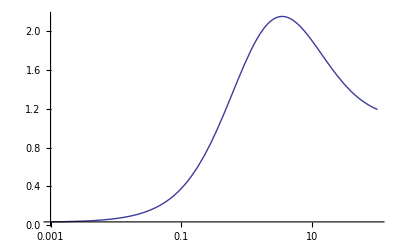

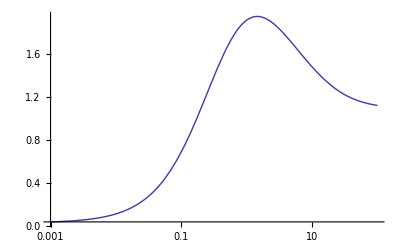

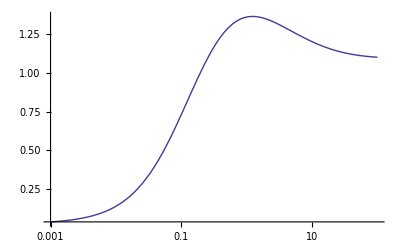

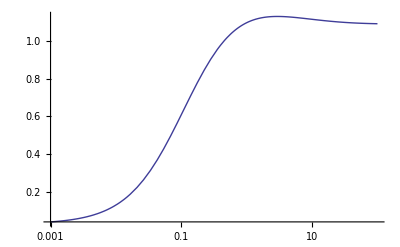

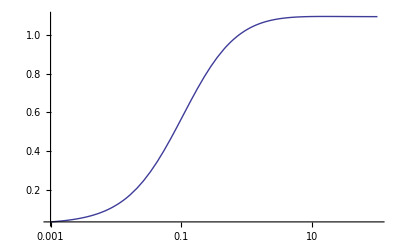

```mathematica
a=5;
b=9;
u1=-3;
u2=6;

w21[ratio_]:=w12 * ratio

(* For a high ratio you get to the state 1 (hidrophilic), for small ratio you get to state 2 (hydrophobic)
Indeed, there is a specific signature in the Angewandte that can be explained only if you do include
fluctuations!!!!*)

w12=0.01;
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21[ratio]],ratio],{ratio,10^(-3),10^(2)},PlotRange->All]
w12=0.1;
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21[ratio]],ratio],{ratio,10^(-3),10^(2)},PlotRange->All]
w12=1;
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21[ratio]],ratio],{ratio,10^(-3),10^(2)},PlotRange->All]
w12=10;
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21[ratio]],ratio],{ratio,10^(-3),10^(2)},PlotRange->All]
w12=100;
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21[ratio]],ratio],{ratio,10^(-3),10^(2)},PlotRange->All]

(*ORIGINAL PLOT
LogLinearPlot[fk[a,b,u1,u2,Abs[-w12-w21],w21/w12],{w21,10^(-3),10^(2)},PlotRange->All]
*)
Clear[a,b,u1,u2,α,β]
```